```mathematica
SetDirectory@NotebookDirectory[]
Needs["FCMLib`",FileNameJoin[{"../lib","FCMLib-cur.wl"}]]
$FCMLibVersion
```

/Users/oosoba/Documents/RAND/Coding/fcm-fusion/lib

Fuzzy Cognitive Map Library ver. 0.0.8

### FCM Combination Demo

```mathematica
nds = {
(*{1,"HCP","Hypercoagulation Positional Factors"},
{2,"stas", "Blood Stasis"},
{3,"inju", "Endothelial Injury"},
{4,"HCF", "Hypercoagulation Factors"}*)
{1,"C1"},
{2,"C2"},
{3,"C3"},
{4,"C4"}
};
nds⟦;;,2⟧ = Map[Style[#, 22,Bold]&, nds⟦;;,2⟧];
(*gspec={{1,2,1},{1,3,-1},{1,4,1},{2,4,-1},{3,1,-1},{3,4,-1},{3,2,1},{4,3,1}};
altGspec={{1,2,1},{1,4,1},{2,4,1},{3,1,-1},{3,2,1},{4,3,1}};

gspec={{1,1,1},{1,2,0.4},{1,3,1}, {1,4,1},{2,3,0.5},{3,2,0.4},{3,4,0.75}};
altGspec={{1,1,1},{1,2,0.4},{1,3,1},{2,3,0.5},{3,2,0.4}};*)

gspec1={{1,1,1},{1,2,1},{1,3,1}, {1,4,1},{2,3,1},{3,2,1},{3,4,1}};
gspec2={{1,1,1},{1,2,1},{1,3,1},{2,3,1},{3,2,1}};
gspec3={{1,2,1},{1,4,1},{2,4,1},{3,1,1}, {4,3,1}}; 


expFCMs = {
FCM[nds,gspec1,0.5],
FCM[nds⟦;;3⟧,gspec2,0.5],
FCM[nds,gspec3,0.5]
};

combFCM =FCMJoin[nds,expFCMs,{2,1,1}];
compfcms = Flatten@{expFCMs, combFCM};
```

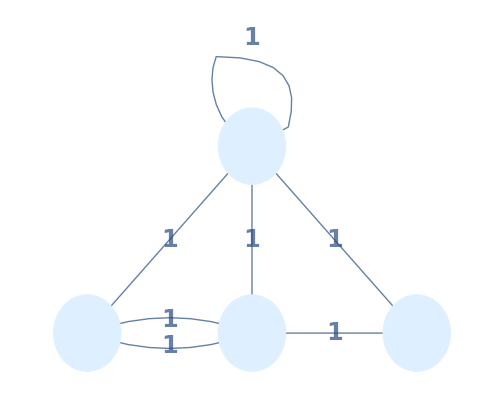
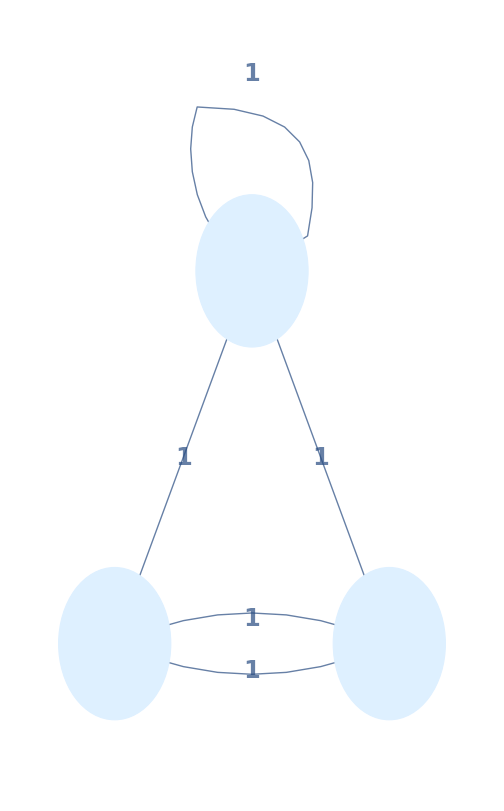
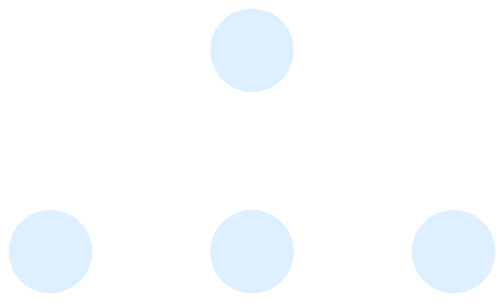
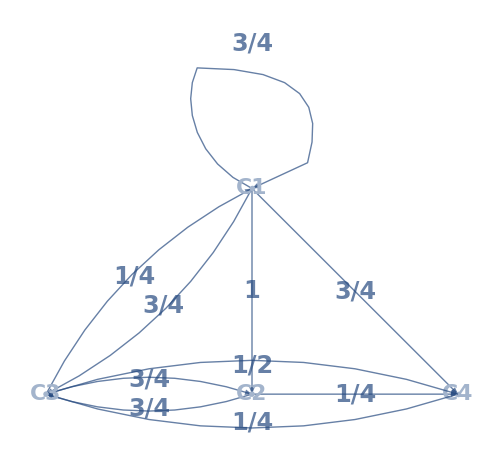

```mathematica
compfcms=Table[
Graph[
f,
GraphLayout->"LayeredDrawing",
EdgeLabelStyle->Directive[24, Bold],
EdgeStyle->Thick,
EdgeShapeFunction->GraphElementData[{"FilledArrow","ArrowSize"->0.073}],
VertexLabels-> (PropertyValue[f, VertexLabels]),
VertexShape->Graphics[{EdgeForm[Thick],LightBlue,Disk[{0,0},0.5×{1.5,1}]}],
ImageSize->72×7
], {f, compfcms}
]
```

```mathematica
expfcms = compfcms⟦;;-2⟧;
candedgs=(EdgeList/@expfcms)
ucands = Sort@Union@Flatten@candedgs


votes=Outer[Boole@Not@FreeQ[candedgs⟦#2⟧,#1]&,ucands, Range@Length@candedgs];
TableForm@votes
```

{{1->1,1->2,1->3,1->4,2->3,3->2,3->4},{1->1,1->2,1->3,2->3,3->2},{1->2,1->4,2->4,3->1,4->3}}

{1->1,1->2,1->3,1->4,2->3,2->4,3->1,3->2,3->4,4->3}

1 | 1 | 0
1 | 1 | 1
1 | 1 | 0
1 | 0 | 1
1 | 1 | 0
0 | 0 | 1
0 | 0 | 1
1 | 1 | 0
1 | 0 | 0
0 | 0 | 1

```mathematica
Total@Transpose@votes
Select[Range@Length@ucands, (Total[Transpose@votes]⟦#⟧<2)&]
vetoed = ucands⟦%⟧
allowed = Complement[ucands, vetoed]
```

{2,3,2,2,2,1,1,2,1,1}

{6,7,9,10}

{2->4,3->1,3->4,4->3}

{1->1,1->2,1->3,1->4,2->3,3->2}

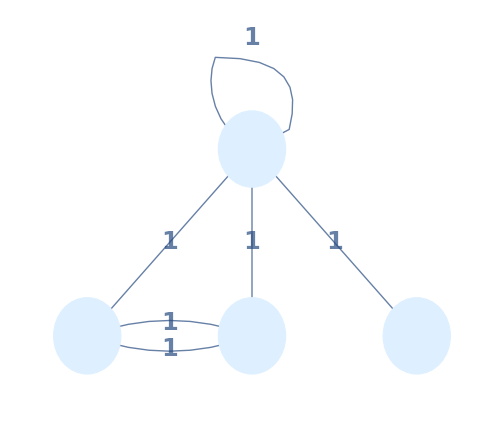
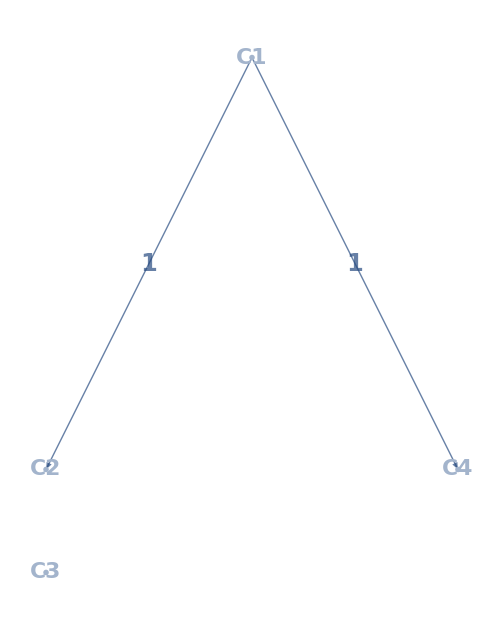
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
updfcms =Table[
EdgeDelete[f,Intersection[EdgeList[f], vetoed]],
{f,expfcms}
]
(*FCMJoin[nds,updfcms,{2,1,1,1}]*)
```

```mathematica
FCMJoinByVote[nodespec_?MatrixQ,fcms_List,wgts_:0,sz_Real:0.25, asz_Real:0.02]:=Module[
	{n=Length@fcms,ws,fincm,newedgs,ucands,candedgs=(EdgeList/@fcms),votes,vetoedLnks},
	ws = If[
		n==Length@wgts,
		(wgts/Total[wgts]),
		ConstantArray[1/n,n]
	];
	ucands = Sort@Union@Flatten@candedgs;
	votes=Outer[Boole@Not@FreeQ[candedgs⟦#2⟧,#1]&,ucands, Range@Length@candedgs]; (*candedgs is __List*)
	vetoedLnks = ucands⟦Select[Range@Length@ucands, (Total[Transpose@votes]⟦#⟧<2)&]⟧;
	fincm = Table[
		EdgeDelete[ f,Intersection[EdgeList[f], vetoedLnks] ], 
		{f,fcms}
	];
	fincm = FCMJoin[nodespec,fincm,ws];
	Return[fincm];
]
```

```mathematica
FCMJoinByVote[nds,expfcms,{2,1,1,1}]
```

```mathematica
Grid[
{compfcms,
Panel/@(Style[#,22]&/@{"Expert #1", "Expert #2", "Expert #3",MatrixForm@FCMat@Last@compfcms})
},
Spacings->{0,0}
]
(*Export["fcm-combo.pdf",%]*)
(*Export["fcm-combo.eps",%]*)
```